```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ψ[x]∈Reals};
```

```mathematica
e[x_]:={Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ψ'[x]}}

```mathematica
b[x_]:={{-ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-1/2 ψ'[x]

```mathematica
H[x_]:=-1/2 ψ'[x]
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:={{{0}}}
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+ H''[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 σ[x] ψ'[x]==κ (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==Cos[ψ[x]],X2'[x]==-Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]],X2'[x]==-Sin[ψ[x]]}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
σ[x_]:=σc
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=1;
ψmax=2.5;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,bcs}],{ψ,X1,X2},{x,xmin,xmax}]
```

{{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}}

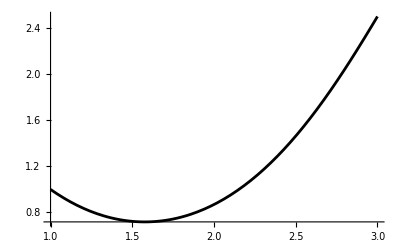

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Black]
```

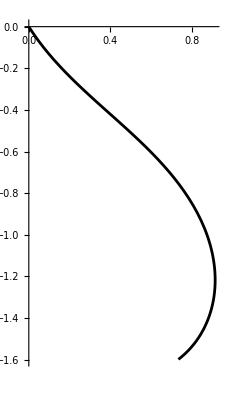

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Black]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,2.26596},{2.8,2.04225},{2.7,1.83222},{2.6,1.63842},{2.5,1.46255},{2.4,1.30559},{2.3,1.16793},{2.2,1.0495},{2.1,0.949975},{2.,0.868857},{1.9,0.80561},{1.8,0.759737},{1.7,0.730829},{1.6,0.718614},{1.5,0.72297},{1.4,0.74394},{1.3,0.781729},{1.2,0.836683},{1.1,0.909264},{1.,1.}}

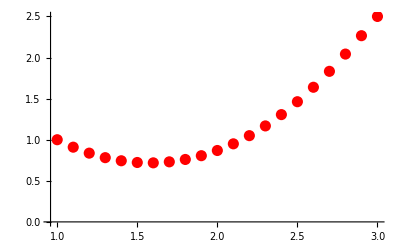

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

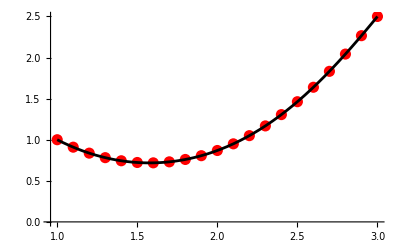

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{0.734976,-1.59923},{0.807403,-1.53048},{0.862324,-1.44706},{0.897992,-1.35376},{0.91421,-1.25518},{0.912023,-1.15528},{0.893311,-1.0571},{0.860386,-0.96273},{0.815675,-0.873321},{0.761504,-0.789294},{0.699972,-0.710487},{0.632915,-0.636315},{0.561913,-0.565905},{0.488328,-0.498193},{0.413366,-0.432007},{0.338145,-0.366115},{0.263764,-0.299277},{0.191378,-0.230286},{0.122269,-0.15802},{0.0579064,-0.0815032},{0.,0.}}

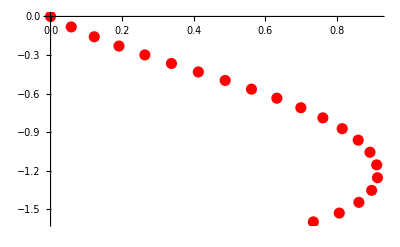

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

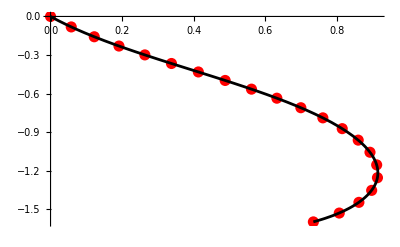

```mathematica
Show[plotXnum,plotXexact]
```

```mathematica
(*plot the normal to the manifold n*)
```

```mathematica
tn=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/n.csv"];
tn=Table[{tn[[i,1]],tn[[i,2]]},{i,2,Length[tn]}]
```

{{0.598415,-0.801293},{0.767974,-0.640536},{0.890941,-0.454172},{0.966044,-0.258438},{0.997724,-0.0675472},{0.994147,0.108057},{0.965032,0.262123},{0.91993,0.392069},{0.867165,0.498008},{0.813392,0.581705},{0.763584,0.645699},{0.721248,0.692669},{0.688726,0.725014},{0.667483,0.744617},{0.658338,0.752715},{0.661611,0.749841},{0.677188,0.735803},{0.704502,0.709694},{0.74242,0.669928},{0.789053,0.61433},{0.841515,0.540324}}

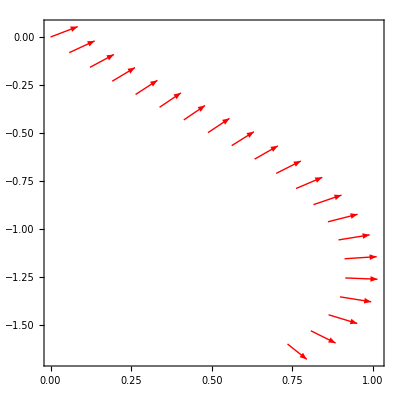

```mathematica
plotn=Graphics[{Red,Table[Arrow[{{tX[[i,1]],tX[[i,2]]},{tX[[i,1]]+0.1*tn[[i,1]],tX[[i,2]]+0.1*tn[[i,2]]}}],{i,1,Length[t]}]},Frame->True,AspectRatio->1,PlotRange->All]
```

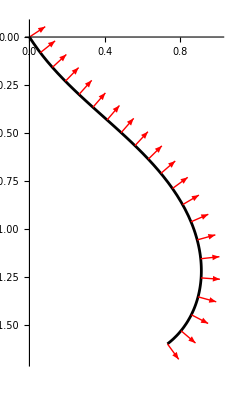

```mathematica
Show[plotXexact,plotn,PlotRange->Full]
```